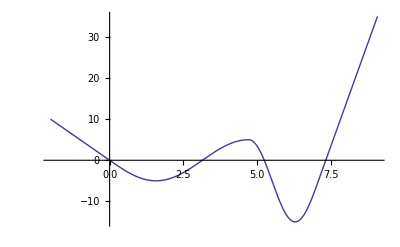

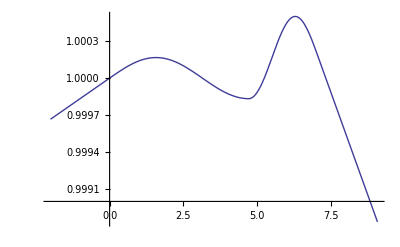

```mathematica
k=10;
T=3000;
a=5;
b=1;
c=10;
d=2;
x1=(3*Pi)/(2*b);
x2=x1+(3*Pi)/(2*d);
shift=a-c-c*d*x2;

f[x_]:=N[If[
x≤0,-a*b*x,
If[
x<x1,
-a*Sin[b*x],
If[
x<x2,
c*(Cos[d*(x-x1)]-1)+a,
c*d*x+shift
]
]
]
];
rho[x_,T_]:=Exp[-f[x]/(k*T)];
Plot[f[x],{x,-2,x2+2}]
Plot[rho[x,T],{x,-2,x2+2}]
```

```mathematica
Block[{$MaxExtraPrecision=1},NIntegrate[rho[x,T],{x,-2,x2+2},MaxRecursion->10,PrecisionGoal->10]
]
```

N::meprec: Internal precision limit $MaxExtraPrecision = 1. reached while evaluating 4 + 9\ π/4 - (4 + 9\ π/4)\ (8 + 9\ π)/16 + 9\ π.

General::stop: Further output of N :: meprec will be suppressed during this calculation.

11.068